### Mapping Gaussian Points

Gaussian integers are prime in only 3 possible cases:
	Case 1:Norm(π) = p and p ≡1 mod 4 
	OR
	Case 2:π = p, p is prime and p ≡3 mod 4
	Case 3: Norm(π) = 2
Any Gaussian integer has 4 associates.  For each π where π = p and p ≡ 1 mod 4, there are 8 total prime Gaussian integers.  For each π = p, p is prime and p ≡ 3 mod 4, there are 4 total prime Gaussian integers
Using the list of primes available in Mathematica, we can easily zero on the Gaussian primes
The trick will be translating the results to all possible corresponding points

### Generating Points for case 1

```mathematica
(*Generate the 8 points with norm = p, it's assumed that p is prime and congruent to 1 mod 4
 PowersRepresentations returns a list of tuples that satisfy the equation.  From a theorem by
 Fermat, the represenation of a prime, p, ≡ 1 mod 4 as a sum of squares is unique, so don't
 need to worry about a list of multiple results *)
mod1SquarePoints[p_, xDistance_] :=
Module[{squares = Flatten[PowersRepresentations[p,2,2]]},
x = squares[[1]];
y = squares[[2]];
If[x <= xDistance && y <= xDistance,
(Sow[{x,y}];Sow[{x,-y}];Sow[{-x,y}];Sow[{-x,-y}];Sow[ {y,x}];Sow[{y,-x}];Sow[{-y,x}];Sow[{-y,-x}])]]

Reap[mod1SquarePoints[1^2 + 14^2, 20]][[2]][[1]]
```

{{1,14},{1,-14},{-1,14},{-1,-14},{14,1},{14,-1},{-14,1},{-14,-1}}

### Generating Points for case 2

```mathematica
mod3SquarePoints[p_] := (Sow[{p,0}];Sow[{-p,0}];Sow[{0,p}];Sow[{0,-p}])

Reap[mod3SquarePoints[7]][[2]][[1]]
```

{{7,0},{-7,0},{0,7},{0,-7}}

### Put the cases together to generate a function for producing Gaussian points Let’s assume you want to display the primes in a given square of size s x s, where the side s has half of it’s length in one quadrant and other half in the adjacent quadrant A prime, p, will correspond to a point p^1/2 from the origin (assuming congruent to 1 mod 4). So if you want a graph that gives you a square of size s x s, the farthest possible point congruent to 1 mod 4 will have norm = (s/2)^2 + (s/2)^2 or 2 * (s/2)^2 For those points corresponding to a prime, p, congruent to 3 mod 4, only find the corresponding points if the prime <= s/2 The max distance you want to explore will determine the primes you want to explore For those primes under case 1, explore primes <= distance^2 since we are using the fact that N(π) = prime, x is the distance, so x = prime^1/2 For those primes under case 2, explore primes <= distance/2 Note, instead of using side length, will use xDistance, this indicates the farthest positive x value on the real line

```mathematica
gaussianSquarePoints[xDistance_] := 
Union[
Reap[
Do[Which[Mod[Prime[i], 4] == 1, mod1SquarePoints[Prime[i], xDistance],Prime[i] ≤ xDistance, mod3SquarePoints[Prime[i]], True, {0,0}],{i, 2, PrimePi[2xDistance^2]}]][[2]][[1]], 
{{1,1},{-1,1}, {1,-1},{-1,-1}}]

gaussianPoints =gaussianSquarePoints[5]
```

{{-5,-4},{-5,-2},{-5,2},{-5,4},{-4,-5},{-4,-1},{-4,1},{-4,5},{-3,-2},{-3,0},{-3,2},{-2,-5},{-2,-3},{-2,-1},{-2,1},{-2,3},{-2,5},{-1,-4},{-1,-2},{-1,-1},{-1,1},{-1,2},{-1,4},{0,-3},{0,3},{1,-4},{1,-2},{1,-1},{1,1},{1,2},{1,4},{2,-5},{2,-3},{2,-1},{2,1},{2,3},{2,5},{3,-2},{3,0},{3,2},{4,-5},{4,-1},{4,1},{4,5},{5,-4},{5,-2},{5,2},{5,4}}

### Iterate through the prime numbers and generate the Gaussian primes How many primes should you use? Assuming for now that we’re generating all possible points in a square, given a side length of s, the farthest possible point from the origin will correspond to a prime congruent to 1 mod 4, and will have norm of 2 * (s/2)^2. We can use the Mathematica PrimePi, function to tell us how many primes are less than or equal to a number. In our case, that number is 2 * (s/2)^2.

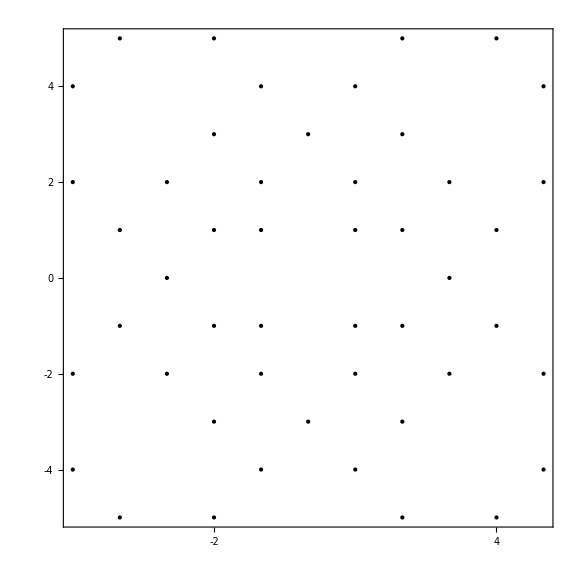

```mathematica
Graphics[Point[gaussianPoints], Frame->True, FrameTicks->{{Range[-10,10,1],None},{Range[-20,20,1],None}}, ImageSize->Large]
```

```mathematica
Manipulate[Graphics[Point[gaussianSquarePoints[z]], Frame->True, FrameTicks->{{Range[-z,z,5],None},{Range[-z,z,5],None}}, ImageSize->Large], {z, 4, 100,2}]
```